```mathematica
infile="/home/daneel/daneelrepo/graphene-hopping/result/data.txt";
data=Import[infile,"Table"];
eplus=Take[data,All,3];
eminus=Drop[data,None,{3}];
ListPlot3D[{eplus, eminus},Mesh->None,InterpolationOrder->3,ColorFunction->"TemperatureMap",AxesLabel->{"k_x","k_y","ϵ_±"},TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]
```

-Graphics3D-

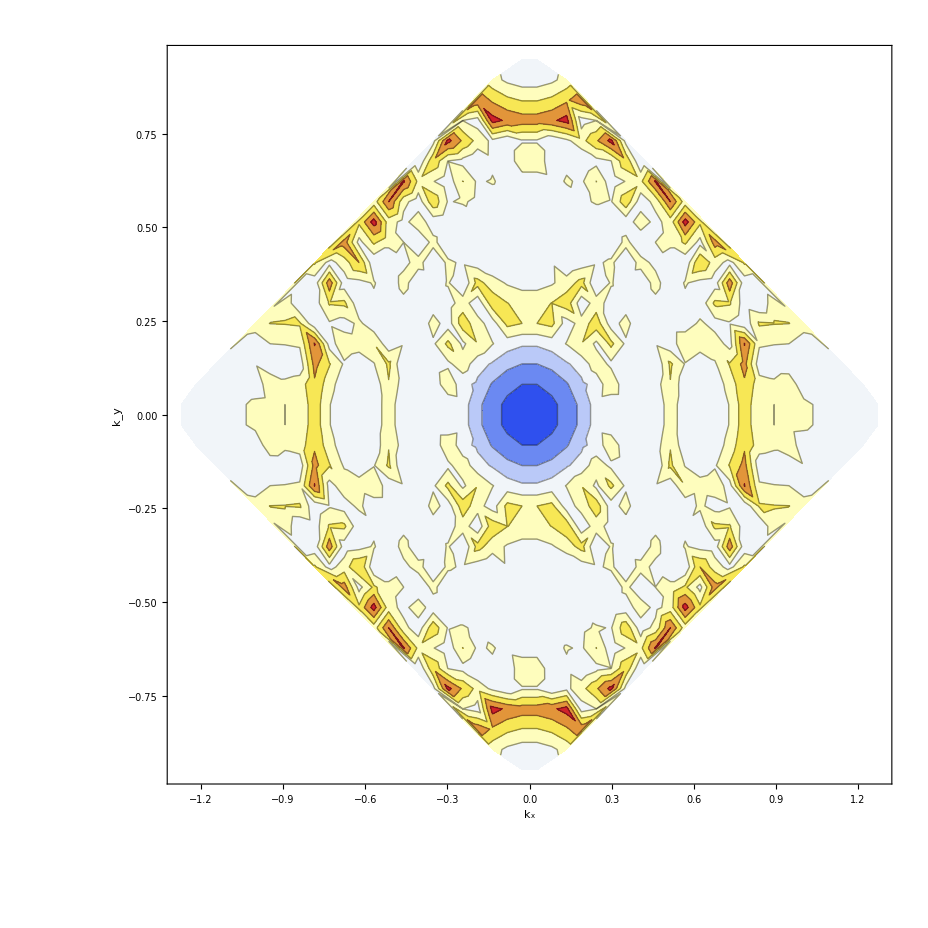

```mathematica
ListContourPlot[eminus,Mesh->None,InterpolationOrder->3,ColorFunction->"TemperatureMap",FrameLabel->{"k_x","k_y"},RotateLabel->False,TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]
```